# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll102`"

methods={"","SemiConstrained","Constrained","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"clean"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
dims={412,176}
```

{412,176}

```mathematica
ims=Table[

tim=1;

nx=1+dims[[1]]*tim*i;
ny=1+dims[[2]]*tim*j;

{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+dims[[2]]*tim},{nx,nx+dims[[1]]*tim}]&/@{ia,ib,id,io}

,{j,Range[0,0]},{i,Range[0,0]}];

max=MinMax[Flatten[ImageData[idd]]][[2]];
Print["max dv=", max]
ImageDimensions[idd]
```

max dv=38.6009

{413,177}

```mathematica
GraphicsGrid[ims[[All,All,1]],Spacings->-2]
```

-Graphics-

```mathematica
ims=Flatten[ims,1];
```

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## More in depth

```mathematica
ImageDimensions[idd]
```

{413,177}

```mathematica
lvl=1;
```

```mathematica
k=100;
{ka,kd}=ImageData[#][[k]]&/@{iaa,idd};
pyra=pyrFuncGen[ka,lvl];

kb=Table[pyra[[1,1]][x+kd[[x]]],{x,1,1+dims[[1]]*tim}];

pyrb=pyrFuncGen[kb,lvl];


pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
(* Test values *)
testLevels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-10,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-10,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
lt=lineTest[n,u,listv0,condition,Range[1,dims[[1]]],pyrab[[1;;1]],e,"ConstrainedCorrelation"];
```

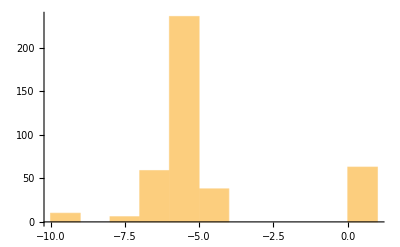

```mathematica
Histogram[Total[#]&/@lt[[All,1;;2]]]
```

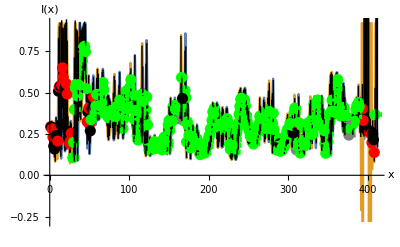

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,dims[[1]]*tim],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

```mathematica
(*pixelIterGraphics[10,1,0,20,{{0.,0.}},condition,5, 1,pyrab[[1;;1]],e,"ConstrainedCorrelation"]*)
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],im[[3]],minmax[[2]],minmax,Range[1,1+dims[[1]]*tim,steps],Range[1,1+dims[[2]]*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@realPVTable[[y]],{y,1,1+dims[[2]]*tim}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
levels={{1,4}};
e=0.0001;
n=0;
u=0;
steps=1;
```

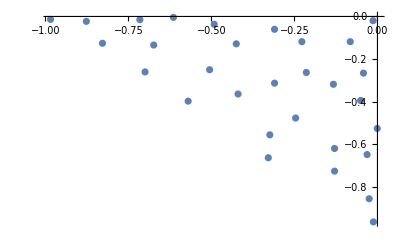

```mathematica
(* Creating list of initial Values *)
range={-10*0.1,0};
listv0=Select[RandomReal[range,{3000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-30];
ListPlot[listv0]
```

```mathematica
(* Creating condition *)
topbot={-10*0.1,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
solution = bigTest[steps,n,u,listv0,condition,e,levels,ims];
```

{10,20}

{20,20}

{30,20}

{40,20}

{50,20}

{60,20}

{70,20}

{80,20}

{90,20}

{100,20}

{110,20}

{120,20}

{130,20}

{140,20}

{150,20}

{160,20}

{170,20}

{180,20}

{10,30}

{190,20}

{20,30}

{30,30}

{200,20}

{40,30}

{210,20}

{50,30}

{10,50}

{60,30}

{20,50}

{220,20}

{30,50}

{70,30}

{230,20}

{40,50}

{80,30}

{50,50}

{90,30}

{10,60}

{240,20}

{60,50}

{20,60}

{100,30}

{70,50}

{30,60}

{110,30}

{250,20}

{80,50}

{40,60}

{120,30}

{90,50}

{50,60}

{260,20}

{60,60}

{100,50}

{130,30}

{270,20}

{10,40}

{70,60}

{280,20}

{20,40}

{110,50}

{80,60}

{140,30}

{30,40}

{90,60}

{290,20}

{120,50}

{40,40}

{100,60}

{150,30}

{130,50}

{300,20}

{50,40}

{110,60}

{60,40}

{310,20}

{160,30}

{140,50}

{120,60}

{70,40}

{320,20}

{10,10}

{150,50}

{170,30}

{80,40}

{130,60}

{20,10}

{330,20}

{90,40}

{180,30}

{160,50}

{30,10}

{140,60}

{40,10}

{190,30}

{100,40}

{340,20}

{170,50}

{150,60}

{50,10}

{110,40}

{60,10}

{200,30}

{180,50}

{350,20}

{160,60}

{120,40}

{70,10}

{210,30}

{80,10}

{190,50}

{130,40}

{170,60}

{360,20}

{220,30}

{90,10}

{140,40}

{200,50}

{100,10}

{370,20}

{180,60}

{230,30}

{110,10}

{150,40}

{210,50}

{190,60}

{380,20}

{240,30}

{120,10}

{200,60}

{160,40}

{220,50}

{390,20}

{250,30}

{210,60}

{130,10}

{170,40}

{230,50}

{400,20}

{260,30}

{140,10}

{220,60}

{240,50}

{180,40}

{410,20}

{270,30}

{150,10}

{230,60}

{250,50}

{190,40}

{280,30}

{260,50}

{200,40}

{160,10}

{240,60}

{290,30}

{210,40}

{170,10}

{270,50}

{250,60}

{180,10}

{300,30}

{220,40}

{280,50}

{260,60}

{190,10}

{310,30}

{230,40}

{200,10}

{290,50}

{270,60}

{320,30}

{210,10}

{240,40}

{300,50}

{280,60}

{330,30}

{220,10}

{250,40}

{290,60}

{340,30}

{310,50}

{230,10}

{260,40}

{300,60}

{350,30}

{320,50}

{270,40}

{240,10}

{310,60}

{280,40}

{360,30}

{330,50}

{320,60}

{250,10}

{290,40}

{330,60}

{370,30}

{260,10}

{340,50}

{340,60}

{380,30}

{300,40}

{350,50}

{270,10}

{350,60}

{310,40}

{390,30}

{360,50}

{280,10}

{360,60}

{320,40}

{400,30}

{290,10}

{370,60}

{370,50}

{410,30}

{330,40}

{300,10}

{380,60}

{380,50}

{310,10}

{340,40}

{390,60}

{390,50}

{320,10}

{350,40}

{400,60}

{400,50}

{330,10}

{410,60}

{360,40}

{410,50}

{340,10}

{370,40}

{350,10}

{380,40}

{360,10}

{390,40}

{370,10}

{400,40}

{410,40}

{380,10}

{390,10}

{400,10}

{410,10}

{10,70}

{20,70}

{30,70}

{40,70}

{50,70}

{60,70}

{70,70}

{80,70}

{90,70}

{100,70}

{110,70}

{120,70}

{130,70}

{140,70}

{150,70}

{160,70}

{170,70}

{180,70}

{190,70}

{200,70}

{210,70}

{220,70}

{230,70}

{240,70}

{250,70}

{260,70}

{270,70}

{280,70}

{290,70}

{300,70}

{310,70}

{320,70}

{330,70}

{340,70}

{350,70}

{360,70}

{370,70}

{10,80}

{20,80}

{380,70}

{30,80}

{390,70}

{40,80}

{50,80}

{400,70}

{60,80}

{410,70}

{70,80}

{80,80}

{90,80}

{10,90}

{100,80}

{20,90}

{30,90}

{40,90}

{110,80}

{50,90}

{60,90}

{120,80}

{70,90}

{130,80}

{80,90}

{90,90}

{140,80}

{150,80}

{100,90}

{160,80}

{110,90}

{170,80}

{10,120}

{120,90}

{20,120}

{180,80}

{130,90}

{30,120}

{190,80}

{140,90}

{40,120}

{200,80}

{50,120}

{150,90}

{10,100}

{60,120}

{210,80}

{160,90}

{20,100}

{70,120}

{30,100}

{220,80}

{10,110}

{170,90}

{20,110}

{40,100}

{80,120}

{230,80}

{50,100}

{180,90}

{30,110}

{60,100}

{40,110}

{190,90}

{240,80}

{90,120}

{200,90}

{70,100}

{50,110}

{100,120}

{250,80}

{210,90}

{80,100}

{60,110}

{260,80}

{110,120}

{270,80}

{120,120}

{90,100}

{70,110}

{220,90}

{280,80}

{130,120}

{100,100}

{80,110}

{230,90}

{290,80}

{110,100}

{140,120}

{90,110}

{240,90}

{300,80}

{120,100}

{250,90}

{150,120}

{100,110}

{310,80}

{260,90}

{160,120}

{130,100}

{320,80}

{110,110}

{270,90}

{140,100}

{330,80}

{170,120}

{120,110}

{150,100}

{280,90}

{340,80}

{180,120}

{130,110}

{160,100}

{290,90}

{350,80}

{190,120}

{140,110}

{170,100}

{300,90}

{360,80}

{200,120}

{180,100}

{150,110}

{310,90}

{190,100}

{370,80}

{210,120}

{160,110}

{320,90}

{220,120}

{380,80}

{200,100}

{230,120}

{330,90}

{390,80}

{170,110}

{210,100}

{400,80}

{340,90}

{240,120}

{180,110}

{220,100}

{410,80}

{250,120}

{350,90}

{190,110}

{230,100}

{260,120}

{200,110}

{360,90}

{240,100}

{270,120}

{370,90}

{210,110}

{280,120}

{250,100}

{380,90}

{220,110}

{290,120}

{260,100}

{390,90}

{300,120}

{230,110}

{270,100}

{400,90}

{310,120}

{240,110}

{280,100}

{320,120}

{410,90}

{250,110}

{290,100}

{330,120}

{260,110}

{340,120}

{300,100}

{270,110}

{350,120}

{360,120}

{310,100}

{370,120}

{280,110}

{380,120}

{320,100}

{390,120}

{290,110}

{400,120}

{330,100}

{410,120}

{300,110}

{340,100}

{310,110}

{350,100}

{320,110}

{330,110}

{360,100}

{340,110}

{370,100}

{380,100}

{350,110}

{360,110}

{390,100}

{370,110}

{400,100}

{380,110}

{410,100}

{390,110}

{400,110}

{10,160}

{410,110}

{20,160}

{30,160}

{40,160}

{50,160}

{60,160}

{70,160}

{80,160}

{90,160}

{100,160}

{110,160}

{120,160}

{130,160}

{140,160}

{150,160}

{160,160}

{170,160}

{180,160}

{190,160}

{200,160}

{210,160}

{220,160}

{230,160}

{240,160}

{250,160}

{260,160}

{270,160}

{280,160}

{290,160}

{300,160}

{310,160}

{320,160}

{330,160}

{340,160}

{350,160}

{360,160}

{370,160}

{380,160}

{390,160}

{400,160}

{410,160}

{10,170}

{20,170}

{30,170}

{40,170}

{50,170}

{60,170}

{70,170}

{80,170}

{90,170}

{100,170}

{110,170}

{120,170}

{130,170}

{140,170}

{150,170}

{160,170}

{170,170}

{180,170}

{190,170}

{200,170}

{210,170}

{220,170}

{230,170}

{240,170}

{250,170}

{260,170}

{270,170}

{280,170}

{290,170}

{300,170}

{310,170}

{320,170}

{330,170}

{340,170}

{350,170}

{360,170}

{370,170}

{380,170}

{390,170}

{400,170}

{410,170}

{10,130}

{20,130}

{30,130}

{40,130}

{50,130}

{60,130}

{70,130}

{80,130}

{90,130}

{100,130}

{110,130}

{120,130}

{130,130}

{140,130}

{150,130}

{160,130}

{170,130}

{180,130}

{190,130}

{200,130}

{210,130}

{220,130}

{230,130}

{10,140}

{240,130}

{20,140}

{250,130}

{260,130}

{30,140}

{10,150}

{40,140}

{270,130}

{20,150}

{280,130}

{50,140}

{30,150}

{290,130}

{60,140}

{40,150}

{300,130}

{70,140}

{50,150}

{310,130}

{80,140}

{60,150}

{320,130}

{90,140}

{330,130}

{70,150}

{340,130}

{100,140}

{80,150}

{350,130}

{110,140}

{360,130}

{90,150}

{120,140}

{370,130}

{100,150}

{380,130}

{130,140}

{390,130}

{400,130}

{110,150}

{140,140}

{410,130}

{120,150}

{150,140}

{130,150}

{160,140}

{140,150}

{170,140}

{150,150}

{180,140}

{160,150}

{190,140}

{170,150}

{200,140}

{180,150}

{210,140}

{190,150}

{220,140}

{200,150}

{230,140}

{210,150}

{240,140}

{220,150}

{250,140}

{230,150}

{260,140}

{240,150}

{270,140}

{250,150}

{280,140}

{290,140}

{260,150}

{300,140}

{270,150}

{310,140}

{280,150}

{320,140}

{290,150}

{300,150}

{330,140}

{340,140}

{310,150}

{350,140}

{320,150}

{360,140}

{330,150}

{370,140}

{340,150}

{350,150}

{380,140}

{360,150}

{390,140}

{370,150}

{400,140}

{380,150}

{410,140}

{390,150}

{400,150}

{410,150}

```mathematica
Print["levelTable Dimensions=",Dimensions[solution]]
```

levelTable Dimensions={1,1,4}

```mathematica
solution[[1,1,1,6]];
```

### Images

```mathematica
Dimensions[ims]
```

{1,4}

```mathematica
imagesTable=Table[

groundTruth=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]]*0.1,scale,{0,1}]]}]];

ConformImages[Rasterize[Image[#],ImageResolution->200]&/@Flatten[{solution[[which,1,4]],groundTruth}],{900}]


,{which,Length[ims]}];
```

```mathematica
im1=GraphicsGrid[Partition[imagesTable[[All,1]],1],Spacings->-2];
im2=GraphicsGrid[Partition[imagesTable[[All,2]],1],Spacings->-2];
```

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
imFinal=Legended[GraphicsRow[{im1,im2},ImageSize->Large,Spacings->-25],legendBar]
```

-Graphics-

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],Rasterize[imFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo102-clean-Full-lvls-im.pdf

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

groundTruth=ImageData[-ims[[which,3]]*0.1];
solution[[which,1,1]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[solution[[which,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim));

vals=Table[
ps=Select[solution[[which,1,1,y,All,All]],1<Round[#[[1]]]<(1.+dims[[1]]*tim)&];
(ps[[All,2]]-groundTruth[[y,Round[ps[[All,1]]]]])^2

,{y,Length[solution[[which,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,0.164777,Density= ,0.297848}}

### Histogram

```mathematica
fontsize=30;
imagesize=500;
maxvalue={{-1.2,0.1},{0,10000}};
```

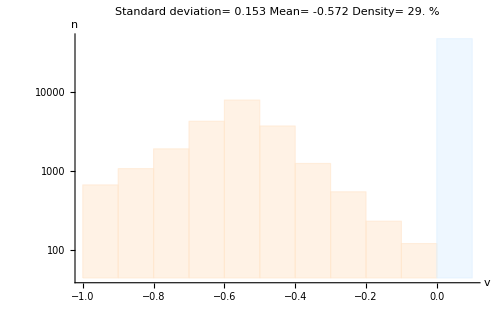

```mathematica
histogramGrid=
Table[

convergedData=Flatten[solution[[idxims,1,1,All,All,2]]];
okData=Flatten[solution[[idxims,1,2,All,All,2]]];
nonConvergedData=Flatten[solution[[idxims,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=((Length[Flatten[DeleteDuplicates[#]&/@Round[solution[[idxims,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim)))*100;

Histogram[{convergedData, nonConvergedData},10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen},TicksStyle->fontsize-6]
,{idxims,Length[ims]}]
```

```mathematica
dims[[1]]*dims[[2]];
Dimensions[convergedData];
```

```mathematica
convergedData=Select[Flatten[ImageData[-ims[[1,3]]*0.1]], topbot[[1]]<#<topbot[[2]]&];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Dimensions[convergedData][[1]]/(dims[[1]]*dims[[2]]))*100.;
```

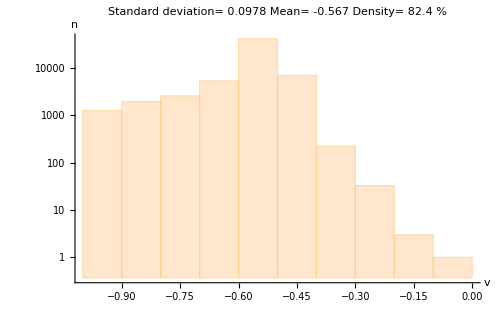

```mathematica
hGroundTruth=Histogram[convergedData,10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},
ChartStyle->{LightOrange},TicksStyle->fontsize-6]
```

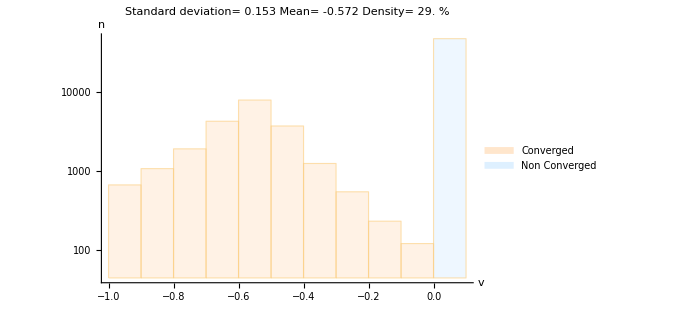
-Graphics--Graphics-

```mathematica
hFinal=Legended[
Row[{histogramGrid[[1]],hGroundTruth}],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{Style["Converged",FontSize->fontsize, FontFamily->"Times",Italic], Style["Non Converged",FontSize->fontsize, FontFamily->"Times",Italic]},LegendLayout->"Row"],Below]]
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-his.pdf"}],Rasterize[hFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo102-clean-Full-lvls-his.pdf